# EigenFunctions

## Tyson Jones tyson.jones@monash.edu August 2017

## WavefunctionSolver Package Test

```mathematica
Clear["Global`*"]
```

## Import

The location of the folder containing the package must be added to the paclet directories

In rare circumstances, the PacletManager` context will not be known, and must be prepended to the below call

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< WavefunctionSolver`
```

The available functions and their options:

```mathematica
?WavefunctionSolver`*
```

## One Dimension

## Normalizing wavefunctions

### constants

Passing a domain means the wavefunction is assumed to drop to 0 from the constant value outside the domain

```mathematica
NormalizeWavefunction[10 ⅈ + 14, {x, 0, 10}]
Integrate[Abs[%]^2, {x, 0, 10}]
```

(7/2+(5 ⅈ)/2)/(√185)

1

```mathematica
NormalizeWavefunction[-4, {-5, 5}]
Integrate[Abs[%]^2, {x, -5, 5}]
```

-1/(√10)

1

Constants normalise to 0 on infinite domains

```mathematica
NormalizeWavefunction[2, {-∞, ∞}]
NormalizeWavefunction[2, {-∞, 4}]
```

0

0

A [0, 1] domain is assumed when a constant and no domain is passed

```mathematica
NormalizeWavefunction[4]
```

4

### vectors

Passing a vector of wavefunction values and a grid-spacing (positive real num) assumes the wavefunction is zero outside the length grid-spacing * (Length[vector] - 1) domain

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},   (* wavefunction values *)
	1                                              (* grid spacing *)
]
1 * Total[ Abs[%]^2]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

1

Passing vectors (wavefunction values and their grid positions; must be consistent/equally-spaced) assumes the wavefunction is zero outside [grid[[1]], grid[[-1]]]

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{0, 1, 2, 3, 4, 5}
]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

Passing a vector of wavefunction values and a domain assumes the wavefunction is zero outside the domain

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{ 0, 5}
]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

(a redundant Symbol can be passed, to clarify the dimension)

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{x, 0, 5}
]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

(any finite vector will normalise to 0 on an infinite domain)

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{ -∞, 5}
]
```

{0,0,0,0,0,0}

Passing no grid-spacing/grid/domain will assume a grid-spacing of 1, and that the wavefunction vanishes outside the length Length[vector]-1 domain

```mathematica
NormalizeWavefunction[
	{1, 2, 3}
]
1 * Total[ Abs[%]^2]
```

{1/(√14),√(2/7),3/(√14)}

1

### functions

A passed function is assumed 0 outside the passed domain

```mathematica
NormalizeWavefunction[
	(Exp[-#^2]&),
	{-1, 1}
]
NIntegrate[Abs[%[x]]^2, {x, -1, 1}]
```

((Exp[-#1^2]&)[#1])/(√1.19629)&

1.

Passing a function and a grid will normalise using (bad) Riemann Summation, sampling the function on the grid

```mathematica
NormalizeWavefunction[
	(Exp[-#^2]&),
	Table[i, {i, -1, 1, .001}]
]
NIntegrate[Abs[%[x]]^2, {x, -1, 1}]
```

((Exp[-#1^2]&)[#1])/(√1.19642)&

0.999887

Passing a function and no domain will result in an assumed (-∞, ∞) domain

```mathematica
NormalizeWavefunction[
	(Exp[-#^2]&),
	{ -∞, ∞}
]
NIntegrate[Abs[%[x]]^2, {x, -∞, ∞}]
```

((Exp[-#1^2]&)[#1])/(√1.25331)&

1.

```mathematica
NormalizeWavefunction[
	Function[x, Exp[-x^2]]
]
```

(Function[x,Exp[-x^2]][#1])/(√1.25331)&

### symbolic expressions

Symbolic expressions are assumed 0 outside the passed domain

```mathematica
NormalizeWavefunction[
	x Exp[-x^2],
	{x, -5, 5}
]

Integrate[Abs[%]^2, {x, -5, 5}]
```

2 ⅇ^(25-x^2) x √(2/(-20+ⅇ^50 √(2 π) Erf[5 √2]))

1

```mathematica
NormalizeWavefunction[
	x Exp[-x^2],
	{x, -∞, ∞}
]

Integrate[Abs[%]^2, {x, -∞, ∞}]
```

2 ⅇ^(-x^2) (2/π)^(1/4) x

1

Passing no domain (passing only the Symbol, or a list containing only a Symbol) will assume a (-∞, ∞) domain

```mathematica
NormalizeWavefunction[x Exp[-x^2], x]
NormalizeWavefunction[x Exp[-x^2], {x}]
```

2 ⅇ^(-x^2) (2/π)^(1/4) x

2 ⅇ^(-x^2) (2/π)^(1/4) x

## Finding eigenmodes

### symbolic

```mathematica
ClearAll[grid, λ, ϕ]
{grid, λ, ϕ} = GetEigenmodes[1/2 x^2, {x, -10, 10}];
```

```mathematica
λ
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5}

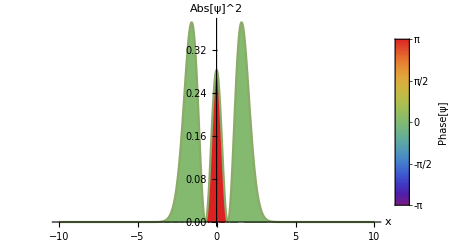

```mathematica
PlotWavefunction[ϕ[[3]], {-10, 10}, PlotRange -> All]
```

```mathematica
(grid[[2]] - grid[[1]]) Total[ Abs[ϕ[[2]]]^2]
```

1.

```mathematica
ClearAll[grid, λ, ϕ]
```

Can pass a low NumberOfPoints to make a terrible approximation

```mathematica
GetEigenmodes[1/2 x^2, {x, -10, 10}, NumberOfModes -> 1, NumberOfPoints -> 10, AutoNormalize -> False]
```

{{-10.,-7.77778,-5.55556,-3.33333,-1.11111,1.11111,3.33333,5.55556,7.77778,10.},{0.732252},{{-2.40593×10^-11,6.08138×10^-6,0.000239875,-0.0176173,-0.706887,-0.706887,-0.0176173,0.000239875,6.08138×10^-6,-2.40594×10^-11}}}

Return InterpolatingFunctions (supported by all other EigenFunctions.m methods) by passing OutputAsFunctions

```mathematica
GetEigenmodes[1/2 x^2, {x, -10, 10}, OutputAsFunctions -> True][[2;;]]
```

{{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5},{InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>]}}

### functions

```mathematica
GetEigenmodes[
	1/2#^2&, { -10, 10}, 
	OutputAsFunctions -> True, 
	NumberOfModes -> 4
][[2;;]]
```

{{0.5,1.5,2.5,3.5},{InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>]}}

### vectors

```mathematica
GetEigenmodes[
	Function[x, 1/2 x^2] /@ Range[-10, 10, .1], { -10, 10}, 
	OutputAsFunctions -> True, 
	NumberOfModes -> 4
][[2;;]]
```

{{0.499999,1.49999,2.49997,3.49993},{InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>]}}

### constants

Note potentials are superposed with an infinite potential well with barriers at the edges of the given domain. Constant passed Potentials are thus really box potentials

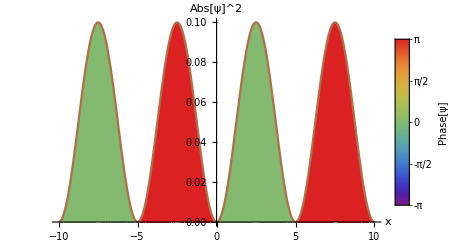

```mathematica
GetEigenmodes[
	4, 
	{-10, 10}
];
PlotWavefunction[%[[3,4]], {-10, 10}]
```

Non-box potentials are effectively approximated by potentials with grow large before the boundaries, on a sufficiently large domain

## Plotting eigenmodes (given)

### vectors

```mathematica
PlotSpectrum[
	{ -5, 5},     (* domain *)
	{1, 1/3, "ⅈ"},  (* eigvals *)
	{{1,1,1,1,1}, {2, 2, 2, 2, 2}, {1.5, 1.5, 1.5, 1.5, 1.5}},  (* eig funcs *)
	PlotRange -> {0,5}
]
```

### functions

```mathematica
PlotSpectrum[
	{x, -5, 5},
	 {1, 2}, 
	{(1&), (2&)},
	 PlotRange -> {0,5},  (* Plot option *)
	Paneled -> True,            (* Manipulate option *)
	LegendLayout -> "Row"  (* BarLegend option *)
	
]
```

### symbolic expressions

```mathematica
PlotSpectrum[
	{x,  -5, 5},
	 {"π", "2π"}, 
	{Exp[-x^2]Exp[x ⅈ],Exp[-x^4]x + .3 ⅈ},
	PlotRange -> {{-2, 2}, {0, 1}}
]
```

### mixed

```mathematica
PlotSpectrum[
	{x,  -5, 5},
	 {1, 2, 4, 5}, 
	{5, x^3, (#&), {1, 2, 3, 4, 5}},
	Paneled -> False
]
```

### wrapped (passing {domain/grid, eigvals, eigfuncs})

Eigenmodes outputs {grid, eigvals, eigfuncs}

```mathematica
PlotSpectrum[
	GetEigenmodes[x^2/2, {x, -10, 10}]
]
```

```mathematica
PlotSpectrum[
	GetEigenmodes[x^2/2, {x, -10, 10}, OutputAsFunctions -> True]
]
```

## Plotting eigenmodes (to be computed)

### functions

```mathematica
PlotSpectrum[
	(#&), {0, 10}, NumberOfPoints -> 100
]
```

### symbolic

```mathematica
PlotSpectrum[
	1/2 x^2, {x, -10, 10},
	PlotRange -> {{-5, 5}, {0, 1}},   (* Plot option *)
	NumberOfModes -> 3,                                 (* GetEigenmodes option *)
	ColorScheme -> "BrightBands",          (* PlotWavefunction option *)
	Paneled -> True,                                       (* Manipulate option *)
	PotentialTransform -> (#/12&),  (* PlotWavefunction options... *)
	PotentialPlotOptions -> {PlotStyle -> Blue}
]
```

### vectors

```mathematica
PlotSpectrum[
	Range[1, 10, .01],
	{0, 10},
	PotentialTransform -> (#/10&)
]
```

### constants

```mathematica
PlotSpectrum[
	0.5,
	{x, 0, 1}
]
```

## Doesn’t match

The same rules of the Potential specification in PlotFunctions.m apply here

```mathematica
PlotSpectrum[x^2, { -10, 10}]
PlotSpectrum[#2&, { -10, 10}]
```

PlotSpectrum[x^2,{-10,10}]

PlotSpectrum[#2&,{-10,10}]

Unequal number of eigenvalues and eigenfunctions

```mathematica
PlotSpectrum[
	{x,  -5, 5},
	 {1, 2, 4, 5, 6}, 
	{x^2, x^3, (#&), {1, 2, 3, 4, 5}},
	Paneled -> False
]
```

PlotSpectrum[{x,-5,5},{1,2,4,5,6},{x^2,x^3,#1&,{1,2,3,4,5}},Paneled→False]

One of the eigenfunctions is symbolic, but a symbol isn’t specified in the domain

```mathematica
PlotSpectrum[
	{-5, 5},
	 {1, 2, 3}, 
	{(#&), x y z, {1, 2, 3, 4, 5}}
]
```

PlotSpectrum[{-5,5},{1,2,3},{#1&,x y z,{1,2,3,4,5}}]

## Throws error

```mathematica
GetEigenmodes[x^2, {x, -5, 5}, poop -> 9];
```

OptionValue::nodef: Unknown option poop for GetEigenmodes.

PlotSpectrum, if passed a potential, accepts options for GetEigenmodes, Manipulate, and all the plotting functions associated with PlotWavefunction

```mathematica
PlotSpectrum[
	1/2 x^2, {x, -10, 10},
	NumberOfModes -> 3, 
	Paneled -> True,
	 poop -> 9
]
```

OptionValue::nodef: Unknown option poop for {PlotWavefunction,BarLegend,Plot,GetEigenmodes,Manipulate}.

However, if passing the eigenfunctions directly, PlotSpectrum will not accept GetEigenmodes options

```mathematica
PlotSpectrum[
	{x, -10, 10},
	{1, 2, 3},
	{x Exp[-x], Exp[-x^2], x Exp[-x^2]},
	NumberOfModes -> 2,
	poop -> 9
]
```

OptionValue::nodef: Unknown option NumberOfModes for {PlotWavefunction,BarLegend,Plot,Manipulate}.

OptionValue::nodef: Unknown option poop for {PlotWavefunction,BarLegend,Plot,Manipulate}.

```mathematica
GetEigenmodes[x^2/2, {x, -10, 10}, NumberOfPoints ->1];
```

GetEigenmodes::numPointsLessThanTwoError: NumberOfPoints given to GetEigenmodes (1) too small; must be at least 2. Using NumberOfPoints -> 10 instead.

```mathematica
GetEigenmodes[x^2/2, {x, -10, 10}, NumberOfPoints ->3, NumberOfModes -> 20];
```

GetEigenmodes::numPointsLessThanNumModes: NumberOfPoints given to GetEigenmodes (3) is less than NumberOfModes (20). Using NumberOfPoints -> 20 instead.

## Two Dimensions